```mathematica
$Assumptions=Element[{a,b},Reals]&&0<γ<Pi/2&&Element[γ,Reals];
```

```mathematica
ScaledAntiHermitianMatrix[a_]:={{I a,1},{-1,I a}};
J[a_,b_,γ_] = (MatrixExp[-I γ/2 KroneckerProduct[ScaledAntiHermitianMatrix[a],ScaledAntiHermitianMatrix[b]]]//TrigToExp//Simplify);
```

```mathematica
J[a,b,γ]//MatrixForm
```

(1/4 (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (1+b) γ)) | 1/4 ⅈ (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)-ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (1+b) γ)) | 1/4 ⅈ (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (1+b) γ)) | 1/4 (-ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (1+b) γ))
-1/4 ⅈ (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)-ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (1+b) γ)) | 1/4 (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (1+b) γ)) | 1/4 (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)-ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (1+b) γ)) | 1/4 ⅈ (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (1+b) γ))
-1/4 ⅈ (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (1+b) γ)) | 1/4 (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)-ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (1+b) γ)) | 1/4 (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (1+b) γ)) | 1/4 ⅈ (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)-ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (1+b) γ))
1/4 (-ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (1+b) γ)) | -1/4 ⅈ (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (1+b) γ)) | -1/4 ⅈ (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)-ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)-ⅇ^(1/2 ⅈ (1+a) (1+b) γ)) | 1/4 (ⅇ^(1/2 ⅈ (-1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (-1+b) γ)+ⅇ^(1/2 ⅈ (-1+a) (1+b) γ)+ⅇ^(1/2 ⅈ (1+a) (1+b) γ)))

## Entanglement

```mathematica
EntanglementMeasure[ψ_List]:=Module[{M,sigma,eigenvals},(*This assumes ψ is normalized*)
M=Partition[ψ,2]; (*Reshape into a 2×2 matrix:rows=first qubit,columns=second qubit*)
sigma=SingularValueList[M]; (*Compute singular values (Schmidt coefficients)*)
eigenvals=DeleteCases[sigma^2,0];(*The squared singular values are the eigenvalues of the reduced density matrix, removing the zeros*)
-Total[Map[# Log[2,#]&,eigenvals]](*Calculate the von Neumann entropy in bits*)
]
```

```mathematica
EntangledState = {1,0,0,0}.J[a,b,γ]//ExpToTrig//FullSimplify;
EntangledState//MatrixForm
EntangledState//TeXForm
```

(ⅇ^(1/2 ⅈ a b γ) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])
ⅇ^(1/2 ⅈ a b γ) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])
ⅇ^(1/2 ⅈ a b γ) (ⅈ Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]+Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])
ⅇ^(1/2 ⅈ a b γ) (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))

\left\{e^{\frac{1}{2} i a b \gamma } \left(\cos \left(\frac{\gamma }{2}\right) \cos
   \left(\frac{a \gamma }{2}\right) \cos \left(\frac{b \gamma }{2}\right)-i \sin
   \left(\frac{\gamma }{2}\right) \sin \left(\frac{a \gamma }{2}\right) \sin
   \left(\frac{b \gamma }{2}\right)\right),e^{\frac{1}{2} i a b \gamma } \left(\cos
   \left(\frac{\gamma }{2}\right) \sin \left(\frac{a \gamma }{2}\right) \cos
   \left(\frac{b \gamma }{2}\right)+i \sin \left(\frac{\gamma }{2}\right) \cos
   \left(\frac{a \gamma }{2}\right) \sin \left(\frac{b \gamma
   }{2}\right)\right),e^{\frac{1}{2} i a b \gamma } \left(\cos \left(\frac{\gamma
   }{2}\right) \cos \left(\frac{a \gamma }{2}\right) \sin \left(\frac{b \gamma
   }{2}\right)+i \sin \left(\frac{\gamma }{2}\right) \sin \left(\frac{a \gamma
   }{2}\right) \cos \left(\frac{b \gamma }{2}\right)\right),e^{\frac{1}{2} i a b
   \gamma } \left(\cos \left(\frac{\gamma }{2}\right) \sin \left(\frac{a \gamma
   }{2}\right) \sin \left(\frac{b \gamma }{2}\right)-i \sin \left(\frac{\gamma
   }{2}\right) \cos \left(\frac{a \gamma }{2}\right) \cos \left(\frac{b \gamma
   }{2}\right)\right)\right\}

```mathematica
entanglement = EntanglementMeasure[EntangledState]//Simplify//PowerExpand//ExpToTrig//Simplify
```

(Log[4 Csc[γ]^2]+2 Cos[γ] Log[Tan[γ/2]])/Log[4]

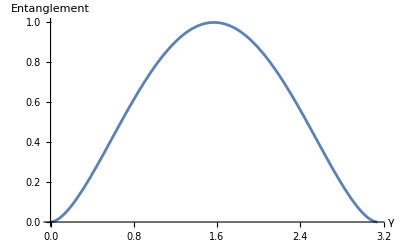

```mathematica
Plot[entanglement,{γ,0,π},AxesLabel->{"γ","Entanglement"}]
```

```mathematica
Maximize[entanglement,γ]//FullSimplify
```

{1,{γ→π/2}}

## Strategy Spaces

### Full SU2

```mathematica
su2[theta_,phi_,psi_]:=Module[{sigma1,sigma2,sigma3,n},(*Define the Pauli matrices*)sigma1={{0,1},{1,0}};
sigma2={{0,-I},{I,0}};
sigma3={{1,0},{0,-1}};
(*Define the unit vector using theta and phi*)n={Sin[theta]*Cos[phi],Sin[theta]*Sin[phi],Cos[theta]};
(*Construct and return the SU(2) matrix*)MatrixExp[-I*(psi/2)*(n[[1]] sigma1+n[[2]] sigma2+n[[3]] sigma3)]]
```

### Rotation Group

```mathematica
rotationGroupTrigRepresentation[n_]:=Module[{r},
r={{Cos[(2π)/n],-Sin[(2π)/n]},{Sin[(2π)/n],Cos[(2π)/n]}};
Table[MatrixPower[r,k],{k,0,n-1}]]

rotationGroupExpRepresentation[n_]:=Module[{r},
r={{E^(I (2 π)/n),0},{0,E^(-I (2 π)/n)}};
Table[MatrixPower[r,k],{k,0,n-1}]]
```

### Dihedral group

```mathematica
dihedralGroupTrigRepresentation[n_]:=Module[{s,rotations,reflections},
s={{0,1},{1,0}};
(*Construct group elements using the new matrices*)rotations=rotationGroupTrigRepresentation[n];reflections=Table[s.r,{r,rotations}];
Join[rotations,reflections]
]

dihedralGroupExpRepresentation[n_]:=Module[{s,rotations,reflections},
s={{0,1},{1,0}};
(*Construct group elements using the new matrices*)rotations=rotationGroupExpRepresentation[n];reflections=Table[s.r,{r,rotations}];
Join[rotations,reflections]
]
```

### Binary Tetrahedral group

```mathematica
binaryTetrahedralGroup:=Module[{qi,qj,qk,q,epsilon,generators,G,newElements,product,nextNew},
(*Define the quaternion representation via 2×2 complex matrices*)
qi={{I,0},{0,-I}};
qj={{0,1},{-1,0}};
qk={{0,I},{I,0}};
q[a_,b_,c_,d_]:=a IdentityMatrix[2]+b qi+c qj+d qk;

(*Define generators:epsilon=(1+i+j+k)/2 and gen2=i (represented by qi)*)epsilon=q[1/2,1/2,1/2,1/2];generators={epsilon,qi};

(*Compute the group closure starting from the identity*)
G={IdentityMatrix[2]};
newElements=generators;

While[newElements!={},nextNew={};
Do[Do[product=Simplify[g1.g2];
If[Not[MemberQ[G,product]],AppendTo[nextNew,product];
AppendTo[G,product];],{g2,generators}],{g1,newElements}];
newElements=nextNew;];

G
]
```

## Playing The Game

```mathematica
play[J_,d1_,d2_]:={1,0,0,0}.J.KroneckerProduct[d1,d2].ConjugateTranspose[J]//ComplexExpand//Simplify//Chop
alicesScore[ψ_]:=((Abs[ψ]^2).{3,0,5,1})//Chop;
bobsScore[ψ_]:=((Abs[ψ]^2).{3,5,0,1})//Chop;
scores[ψ_]:={alicesScore[ψ],bobsScore[ψ]};
```

#### Testing the classical cases

```mathematica
cooperateMove = IdentityMatrix[2];
defectMove = {{0,1},{-1,0}};
classicalMoves = {cooperateMove,defectMove};
```

Classical Payoff matrix for Allice

```mathematica
Table[alicesScore[play[J[0,0,0],m1,m2]],{m1,classicalMoves},{m2,classicalMoves}]//MatrixForm
```

(3 | 0
5 | 1)

Classical Payoff matrix for Bob

```mathematica
Table[bobsScore[play[J[0,0,0],m1,m2]],{m1,classicalMoves},{m2,classicalMoves}]//MatrixForm
```

(3 | 5
0 | 1)

## Identifying Nash Equilibria

```mathematica
numericNashEquilibria[A_,B_]:=Module[{m,n,eqs},
{m,n}=Dimensions[A];

eqs=Select[Flatten[Table[{i,j},{i,m},{j,n}],1],With[{i0=#[[1]],j0=#[[2]]},AllTrue[Range[m],(If[#==i0,True,A[[#,j0]]<=A[[i0,j0]]])&]&&AllTrue[Range[n],(If[#==j0,True,B[[i0,#]]<=B[[i0,j0]]])&]]&];

eqs/. {i_,j_}:>{{i,j},A[[i,j]],B[[i,j]]}]
```

```mathematica
symbolicNashEquilibria[A_,B_]:=Module[{m,n,eqs={},cond1,cond2,sol},{m,n}=Dimensions[A];
Do[(*Player 1:no row deviation improves payoff*)cond1=And@@Table[A[[i0,j0]]>=A[[i,j0]],{i,m}];
(*Player 2:no column deviation improves payoff*)cond2=And@@Table[B[[i0,j0]]>=B[[i0,j]],{j,n}];
sol=Reduce[cond1&&cond2,assumptions];
If[sol=!=False,AppendTo[eqs,{{i0,j0},sol}]],{i0,m},{j0,n}];
eqs]
```

## Example

```mathematica
strategySpace = dihedralGroupTrigRepresentation[4];
n = Length[strategySpace];
finalStates = Table[play[J[a,b,γ],s1,s2],{s1,strategySpace},{s2,strategySpace}];
alicesScores = Table[alicesScore[finalStates[[i,j]]],{i,n},{j,n}];
bobsScores = Table[bobsScore[finalStates[[i,j]]],{i,n},{j,n}];
```

```mathematica
Manipulate[Module[{matA,matB,m,n,neCells,commonOpts,verticalLines,horizontalLines,nashRects,ne},(*Compute payoff matrices and dimensions*)matA=alicesScores/. {a->A,b->B,γ->Γ};
matB=bobsScores/. {a->A,b->B,γ->Γ};
{m,n}=Dimensions[matA];
(*Find pure Nash equilibria*)
ne =numericNashEquilibria[matA,matB]; 
neCells=ne[[All,1]];
(*Common plot options so we only set them once*)commonOpts={ColorFunction->(Blend[{{0,White},{5,Blue}},#]&),ColorFunctionScaling->False};
(*Build vertical lines for first plot (center of columns)*)horizontalLines=Table[Line[{{j-0.5,0},{j-0.5,m}}],{j,1,n}];
(*Build horizontal lines for second plot (center of rows)*)verticalLines=Table[Line[{{0,m-i+0.5},{n,m-i+0.5}}],{i,1,m}];
(*Red rectangles for Nash equilibria*)nashRects=Table[With[{i=cell[[1]],j=cell[[2]]},Rectangle[{j-1,m+1-i-1},{j,m+1-i}]],{cell,neCells}];
{MatrixPlot[matA,Evaluate@commonOpts,Epilog->{Black,Thin,verticalLines,(*Thin black vertical lines*)EdgeForm[Directive[Red,Thick]],FaceForm[None],nashRects                            (*Red squares for NE*)}],MatrixPlot[matB,Evaluate@commonOpts,Epilog->{Black,Thin,horizontalLines,(*Thin black horizontal lines*)EdgeForm[Directive[Red,Thick]],FaceForm[None],nashRects                            (*Red squares for NE*)}],ne}],{A,0.,10.},{B,0.,10.},{{Γ,Pi/5},0,Pi/2}]
```

## Example

```mathematica
strategySpace = dihedralGroupExpRepresentation[4];
n = Length[strategySpace];
finalStates = Table[play[J[a,b,γ],s1,s2],{s1,strategySpace},{s2,strategySpace}];
alicesScores = Table[alicesScore[finalStates[[i,j]]],{i,n},{j,n}];
bobsScores = Table[bobsScore[finalStates[[i,j]]],{i,n},{j,n}];
```

```mathematica
Manipulate[Module[{matA,matB,m,n,neCells,commonOpts,verticalLines,horizontalLines,nashRects,ne},(*Compute payoff matrices and dimensions*)matA=alicesScores/. {a->A,b->A,γ->Γ};
matB=bobsScores/. {a->A,b->A,γ->Γ};
{m,n}=Dimensions[matA];
(*Find pure Nash equilibria*)
ne =numericNashEquilibria[matA,matB]; 
neCells=ne[[All,1]];
(*Common plot options so we only set them once*)commonOpts={ColorFunction->(Blend[{{0,White},{5,Blue}},#]&),ColorFunctionScaling->False};
(*Build vertical lines for first plot (center of columns)*)horizontalLines=Table[Line[{{j-0.5,0},{j-0.5,m}}],{j,1,n}];
(*Build horizontal lines for second plot (center of rows)*)verticalLines=Table[Line[{{0,m-i+0.5},{n,m-i+0.5}}],{i,1,m}];
(*Red rectangles for Nash equilibria*)nashRects=Table[With[{i=cell[[1]],j=cell[[2]]},Rectangle[{j-1,m+1-i-1},{j,m+1-i}]],{cell,neCells}];
{MatrixPlot[matA,Evaluate@commonOpts,Epilog->{Black,Thin,verticalLines,(*Thin black vertical lines*)EdgeForm[Directive[Red,Thick]],FaceForm[None],nashRects                            (*Red squares for NE*)}],MatrixPlot[matB,Evaluate@commonOpts,Epilog->{Black,Thin,horizontalLines,(*Thin black horizontal lines*)EdgeForm[Directive[Red,Thick]],FaceForm[None],nashRects                            (*Red squares for NE*)}],ne}],{A,0.,10.},{A,0.,10.},{Γ,0,2 ArcTan[√(5-2 √6)]}]
```

```mathematica
(numericNashEquilibria[alicesScores/.{a->0,b->0,γ-> 2 ArcTan[√(5-2 √6)]},bobsScores/.{a->0,b->0,γ-> 2 ArcTan[√(5-2 √6)]}]//Simplify)
```

{{{5,6},5/3,5/3},{{5,8},5/3,5/3},{{6,5},5/3,5/3},{{6,7},5/3,5/3},{{7,6},5/3,5/3},{{7,8},5/3,5/3},{{8,5},5/3,5/3},{{8,7},5/3,5/3}}

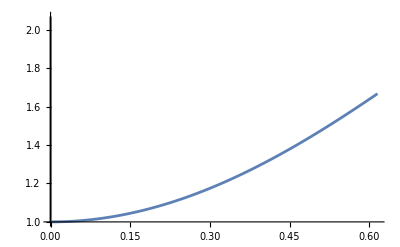

```mathematica
Plot[(numericNashEquilibria[alicesScores/.{a->0,b->0,γ-> G},bobsScores/.{a->0,b->0,γ-> 2 ArcTan[√(5-2 √6)]}]//Simplify)[[1,2]],{G,0,2 ArcTan[√(5-2 √6)]}]
```

```mathematica
neConditions = symbolicNashEquilibria[alicesScores/.{a->0,b->0}//Simplify,bobsScores/.{a->0,b->0}//Simplify]//Simplify;
```

```mathematica
Reduce[(Or@@DeleteDuplicates[neConditions[[All,2]]][[2;;]])&&0<γ<Pi/2,γ]//Simplify
```

γ≤2 ArcTan[√(5-2 √6)]